# Constraint-based modeling

The following sections provide a very general introduction into the constraint-based modeling capabilities of the toolbox. More detailed information can be obtained from the individual documentation pages of the respective commands. A primer and a review of constraint-based modeling can be found herehttp://www.nature.com/nbt/journal/v28/n3/full/nbt.1614.html or herehttp://www.nature.com/nrmicro/journal/v2/n11/abs/nrmicro1023.html.

Load the package

```mathematica
Needs["Toolbox`"]
```

Load a model of Escherichia coli central metabolism

```mathematica
ecoli=ExampleData[{"Toolbox","EcoliCore"}];
```

### Constraints

Constraint-based modeling evaluates phenotypes in the light of biological, physical, and chemical constraints. One important type of constraints are flux capacities, e.g, a reaction is irrversible under physiological conditions and can thus carry only positive net-flux. Toolbox models provide a Constraintspaclet:Toolbox/ref/Constraints attribute where this kind of information can be included. Lower and upper bounds on reactions fluxes are encoded using rules of flux identifiers and pairs of

v_id→{lowerBound, upperBound} | Single flux constraint
getConstraints[model] or model["Constraints"] | access the model constraints
setConstraints[model, constr] | overwrite previous constraints with new constraints (constr)
updateConstraints[model, constr] | udpate existing constraints with new constraints (constr)

Dealing with constraints

Query all available constraints.

```mathematica
ecoli["Constraints"]
```

-Graphics-

Looking at the flux bounds of all availabe exchange reactions reveals that the current model can only infinitely secrete but not take up any matter.

```mathematica
SlideView[#->(v[getID[#]]/.ecoli["Constraints"])&/@getExchanges[ecoli]]
```

Change a few exchange reaction flux bounds to reflect an aerobic minimal glucose medium.

```mathematica
updateConstraints[ecoli,{Subscript[v, EX_glc(e)]->{-∞,10},Subscript[v, EX_o2(e)]->{-∞,∞},Subscript[v, EX_pi(e)]->{-∞,∞},Subscript[v, EX_h(e)]->{-∞,∞},Subscript[v, EX_nh4(e)]->{-∞,∞}}];
```

### Flux-balance and flux-variability analysis

Flux-balance analysis (FBA) finds a steady-state flux solution that maxmizes a cellular objective, e.g., optimal growth rate. For example, FBA can be used to asses the consequence of genetic perturbations. Flux-variablity analysis (FVA) calculates effective flux bounds by minimizing and maximizing flux through individual reactions. For example, FBA solutions are rarely unique and FVA can be used to assess the space of alternativa optimal solutions.

fba[model, obj] | find a steady-state flux distribution that maximizes obj
fva[model] | find minimum and maximum fluxes for all reactions in model

Basic COBRA functionality

Perform FBA.

```mathematica
obj=Subscript[v, Biomass_Ecoli_core_N(w/GAM)_Nmet2];
fluxes=fba[ecoli,obj]//Chop
```

-Graphics-

Visualize the fluxes on a pathway map.

```mathematica
{cmpd,rxns,text}=ExampleData[{"Toolbox","EcoliCoreMap"}];
drawPathway[cmpd,rxns,Flatten@text,ReactionData->Select[fluxes,#[[2]]≠0&],PlotLegends->{LegendLabel->"Flux\nmmol h^-1 gDW^-1"}]
```

-Graphics-

Perform FVA.

```mathematica
fvaSol=fva[ecoli]//Chop
```

-Graphics-

Visualize FVA result.

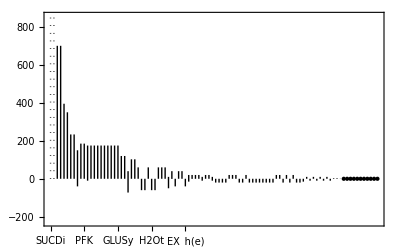

```mathematica
plotFVA[fvaSol]
```

### High-throughput data integration

In progress ...

gimme[...] | find a steady-state flux distribution that maximizes obj and matches data

XXXX.

Perform GIMME

```mathematica
gimme[ecoli, data]
```

### Changing linear programming solver back-ends

Per default, the toolbox uses Mathematica's built-in linerar programming solver (LinerarProgramming). Depending on the availability of other optimization tools, different solver back-ends can be used to solve constraint-based modeling problems.

LinearProgramming | Mathematica's internal linear programming solver
GurobiSolve | MathLink interface to Gurobi
GLPKStandalone | Interface to the GLPK standalone solver
CPLEXStandalone | Interface to the CPLEX standalone solver

Supported solver back-ends

Use GLPKStandalone instead of LinearProgramming

```mathematica
fba[ecoli,obj,Solver->CPLEXStandalone]//Short
```

{v_ACALD→0,v_ACALDt→0,v_ACKr→0,v_ACONTa→5.12759,«90»,v_(EX_succ(e))→0,v_GLYK→0,v_G3PD2→0,v_(EX_glyc(e))→0}